```mathematica
Quit[]
```

README:
This Notebook contains the calculations performed in Appendix C of arXiv:2605.16168.

In that article, we find solutions to consistent truncations of supergravity where some real scalars are analytically extended to imaginary values, ensuring the metric remains real-valued. Among the solutions there are Lorentzian traversable wormholes connecting two asymptotically Anti-de Sitter spacetimes and flows that have a real metric also when uplifted to ten or eleven dimensions. We argue that the holographic duals are pseudo-Hermitian and PT-symmetric theories. Wormhole solutions also admit an interpretation as the low-energy theory of two stacks of branes and antibranes after tachyon condensation. The wormhole is then dual to an entangled state of two copies of the theory that lives on a stack of branes. We present some evidence by computing the mutual information between the theories at each boundary and by identifying the Goldstone bosons associated to the breaking of the two copies of Poincaré symmetry to their diagonal subgroup.

Even though the solutions we construct satisfy a set of BPS equations and can be seen as analytic extensions of supersymmetric solutions, their stability is not guaranteed. In this Notebook we study the perturbative stability of 3 examples of ghost scalars coupled to gravity, listed in the section 2.2 of arXiv:2605.16168. 

In the Examples 1 and 2 that we examine, we find no evidence of instability. In Example 5 we find an unstable mode.

The methodology is briefly explained at the start of each example and in much more detail in Appendix B and C of arXiv:2605.16168.

Authors of the article: Jose M. Begines, Antón F. Faedo, Carlos Hoyos, Daniele Musso
Developers of the Notebook: Carlos Hoyos, Daniele Musso

Notation:
- The squared mass M^2 of the paper is denoted in the present notebook with λ.

Each example constitutes an independent code. Quit the kernel before running.

# Stability Analysis

d+1=5 Wormholes 𝒩==4 SYM Coulomb branch (Example 1)

Methodology:
We employ a spectral method based on Chebyshev polynomials.

We first compactify the radial domain introducing a coordinate υ ∈ [-1,1]. The resulting ODE has a singular point at υ = 0, which requires us to split the problem into two subdomains, υ ∈ [-1,0] and υ ∈ [0,1]. Since the two subproblems are identical, we restrict our analysis to the negative-υ domain. The solution in the positive-υ  domain is determined by parity.

We then analyze the asymptotic behavior of the solutions at the two endpoints, υ = -1 and υ = 0. This allows us to explicitly factor out the corresponding asymptotic behavior at each endpoint. We subsequently introduce a new radial coordinate s ∈ [-1,1], which provides the standard domain for the Chebyshev expansion. 

The radial domain is discretized on a Gauss-Lobatto grid. This yields a convenient and efficient construction of discretized radial first- and second-order derivatives. Since the regular asymptotics have been factored out, no additional boundary conditions need to be imposed. The spectrum is then obtained by solving the resulting discretized generalized eigenvalue problem.

## Background

Superpotential:

```mathematica
W[η_]=6/L Cos[η/(√3)];
```

Potential from superpotential:

```mathematica
d=4;
V[η_]=-1/2 W'[η]^2-d/(4(d-1))W[η]^2//Simplify
```

-(3 (3+Cos[(2 η)/(√3)]))/L^2

Background profile of the scalar ghost:

```mathematica
η0[r_]=2 √3 ArcTan[ⅇ^(2(r-r0)/L)];
```

For convenience, we define the warp factor as a(r)≡e^(2A(r)), with

```mathematica
a[r_]=2 Cosh[(2 (r-r0))/L];
```

## Z_η fluctuation

Equation of motion. We define the dimensionless eigenvalue λ≡L √(ω^2-k^2):

```mathematica
eqZη=Zη''[r]+(2 a'[r])/a[r] Zη'[r]+((w^2-k^2)/a[r]-(4 a[r] V'[η0[r]] η0'[r])/(3 a'[r])-4/3 η0'[r]^2-(2 a[r]^2 η0'[r]^4)/(9 a'[r]^2)+V''[η0[r]])Zη[r] /.w->(√(λ+L^2 k^2))/L//TrigToExp//Simplify
```

((4 ⅇ^((12 r)/L)+4 ⅇ^((12 r0)/L)-36 ⅇ^((4 (2 r+r0))/L)-36 ⅇ^((4 (r+2 r0))/L)-2 ⅇ^((6 (r+r0))/L) λ+ⅇ^((2 (5 r+r0))/L) λ+ⅇ^((2 (r+5 r0))/L) λ) Zη[r])/((ⅇ^((4 r)/L)-ⅇ^((4 r0)/L))^2 (ⅇ^((4 r)/L)+ⅇ^((4 r0)/L)) L^2)+(4 (ⅇ^((4 r)/L)-ⅇ^((4 r0)/L)) Zη'[r])/((ⅇ^((4 r)/L)+ⅇ^((4 r0)/L)) L)+Zη''[r]

Change of radial coordinate (compactification):

```mathematica
rv[v_]=r0+L Log[(1+v)/(1-v)]; (* old coordinate as a function of the new coordinate *)
vr[rr_]=Solve[ⅇ^((rr-r0)/L)==(1+v)/(1-v),v][[1,1,2]]; (* new coordinate as a function of the old coordinate *)
Zη[r_]=zη[vr[r]];

eqzη=Collect[Simplify[(4 L^2)/((v^2-1)^2)eqZη/.r->rv[v]],{zη''[v],zη'[v],zη[v],λ},FullSimplify]
```

((-2+24 v^2+20 v^4+24 v^6-2 v^8)/(v^2 (-1+v^4)^2)+(2 λ)/(1+6 v^2+v^4)) zη[v]+(2 v (-15-10 v^2+v^4) zη'[v])/(-1-5 v^2+5 v^4+v^6)+zη''[v]

The equation is singular in v==0. The problem splits in two identical subproblems, negative v∈[-1,0] and positive v∈[0,1]. Let us consider the negative subproblem.

```mathematica
c1=Coefficient[eqzη,zη'[v]];
c0=Coefficient[eqzη,zη[v]];
```

Asymptotic study about v==-1:

```mathematica
c1vm1=Series[c1,{v,-1,-1}]
c0vm1=Series[c0,{v,-1,-2}]

DSolve[zη''[v]+Normal[c1vm1] zη'[v]+Normal[c0vm1] zη[v]==0,zη[v],v]//Flatten
```

-3/(v+1)+O[v+1]^0

4/(v+1)^2+1/O[v+1]

{zη[v]→(1+v)^2 C[1]+2 (1+v)^2 C[2] Log[1+v]}

Asymptotic study about v==0:

```mathematica
c1v0=Series[c1,{v,0,-1}]
c0v0=Series[c0,{v,0,-2}]

DSolve[zη''[v]+Normal[c1v0] zη'[v]+Normal[c0v0] zη[v]==0,zη[v],v]//Flatten
```

O[v]^1

-2/v^2+1/O[v]

{zη[v]→C[1]/v+v^2 C[2]}

Modes ~ 1/v are odd and modes ~ v^2 are even

We factor out explicitly the normalizable behaviours at both asymptotic regions and fix the even or odd parity:

```mathematica
eqzηe=eqzη/.zη->zηe;
eqzηo=eqzη/.zη->zηo;
```

```mathematica
zηe[v_]=v^2(1-v^2)^2 ψve[v];
zηo[v_]=1/v(1-v^2)^2 ψvo[v];
```

We change the radial coordinate so that the domain coincides with the domain of Chebyshev polynomials s∈[-1,1]. We also multiply the equation for the singular factor (1-s^2). We ensure that the parity of the solution is fixed.

```mathematica
vs[s_]=-Sqrt[(1-s)/2];
ψve[v_]=ψe[1-2 v^2];
ψvo[v_]=ψo[1-2 v^2];
```

```mathematica
eqψe=Collect[((1-s)(1+s)eqzηe/.v->vs[s])/Coefficient[eqzηe/.v->vs[s],ψe''[s]],{ψe''[s],ψe'[s],ψe[s],λ},FullSimplify]
```

((2 (61+s (258+s (-248+(62-5 s) s))))/((-3+s)^2 (17+(-14+s) s))+((1+s) λ)/(17+(-14+s) s)) ψe[s]+((-107+s (-69+(151-15 s) s)) ψe'[s])/(34+2 (-14+s) s)+(1-s^2) ψe''[s]

```mathematica
eqψo=Collect[((1-s)(1+s)eqzηo/.v->vs[s])/Coefficient[eqzηo/.v->vs[s],ψo''[s]],{ψo''[s],ψo'[s],ψo[s],λ},FullSimplify]
```

(-5/2+16/(-3+s)^2+4/(-3+s)-(32 (-1+s))/(17+(-14+s) s)+((1+s) λ)/(17+(-14+s) s)) ψo[s]+((-5+s (-51+(73-9 s) s)) ψo'[s])/(34+2 (-14+s) s)+(1-s^2) ψo''[s]

## Numerics, even modes (Chebyshev spectral method)

We define the coefficients of the discretized matrix.

```mathematica
Clear[A0,A1,B0,B1,S0];

S0[s_]=Coefficient[eqψe,ψe''[s]];
A0[s_]=Coefficient[eqψe,ψe'[s]]/.λ->0;
A1[s_]=Coefficient[Coefficient[eqψe,ψe'[s]],λ];
B0[s_]=Coefficient[eqψe,ψe[s]]/.λ->0;
B1[s_]=Coefficient[Coefficient[eqψe,ψe[s]],λ];
```

Gauss-Lobatto grid:

```mathematica
chebGrid[n_]:=N[Cos[Pi Range[0,n]/n],100];
```

Matrices for first and second derivative:

```mathematica
chebD[n_,prec_: MachinePrecision]:=Module[{x,c,D,X,C,dX},
x=N[Cos[Pi Range[0,n]/n],prec];
c=Join[{2},ConstantArray[1,n-1],{2}]*(-1)^Range[0,n];
(*Build matrices*)
X=Outer[Subtract,x,x];
C=Outer[Times,c,1/c];
(*Add identity to avoid division by zero*)
dX=X+IdentityMatrix[n+1];
D=C/dX;
(*Fix diagonal*)
D=D-DiagonalMatrix[Total[D,{2}]];
D]
```

Discretized problem:

```mathematica
buildMatrices[NN_]:=Module[{s,S0v,A0v,A1v,B0v,B1v,M0,M1,n1},(*Work with packed interior grid*)
n1=NN+1;
s=Developer`ToPackedArray[chebGrid[NN]];
(*Vectorized evaluation (no Table!)*)
S0v=Developer`ToPackedArray[S0/@s];
A0v=Developer`ToPackedArray[A0/@s];
A1v=Developer`ToPackedArray[A1/@s];
B0v=Developer`ToPackedArray[B0/@s];
B1v=Developer`ToPackedArray[B1/@s];
(*Replace DiagonalMatrix[v].D with fast row scaling*)
D1=chebD[NN,100];
D2=D1.D1;
M0=S0v*D2+A0v*D1;
M0=M0+DiagonalMatrix[B0v];
M1=A1v*D1+DiagonalMatrix[B1v];

{M0,M1}]
```

Function which computes of the first ten eigenvalues for M^2 in the normal mode spectrum:

```mathematica
computeQNMs[NN_]:=Module[{M0,M1,vals},{M0,M1}=buildMatrices[NN];
vals=Eigenvalues[{M0,-M1},-10];
vals];
```

First 10 eigenvalues M^2 computed with 100 and 200 collocation points:

```mathematica
modes100=N[Sort[computeQNMs[100]],5]
```

{13.397,53.933,117.15,203.3,312.41,444.48,599.52,777.53,978.51,1202.5}

```mathematica
modes200=N[Sort[computeQNMs[200]],5]
```

{13.397,53.933,117.15,203.3,312.41,444.48,599.52,777.53,978.51,1202.5}

## Numerics and zero mode, odd modes (Chebyshev spectral method)

We define the coefficients of the discretized matrix.

```mathematica
Clear[A0,A1,B0,B1,S0];

S0[s_]=Coefficient[eqψo,ψo''[s]];
A0[s_]=Coefficient[eqψo,ψo'[s]]/.λ->0;
A1[s_]=Coefficient[Coefficient[eqψo,ψo'[s]],λ];
B0[s_]=Coefficient[eqψo,ψo[s]]/.λ->0;
B1[s_]=Coefficient[Coefficient[eqψo,ψo[s]],λ];
```

Gauss-Lobatto grid:

```mathematica
chebGrid[n_]:=N[Cos[Pi Range[0,n]/n],100];
```

Matrices for first and second derivative:

```mathematica
chebD[n_,prec_: MachinePrecision]:=Module[{x,c,D,X,C,dX},
x=N[Cos[Pi Range[0,n]/n],prec];
c=Join[{2},ConstantArray[1,n-1],{2}]*(-1)^Range[0,n];
(*Build matrices*)
X=Outer[Subtract,x,x];
C=Outer[Times,c,1/c];
(*Add identity to avoid division by zero*)
dX=X+IdentityMatrix[n+1];
D=C/dX;
(*Fix diagonal*)
D=D-DiagonalMatrix[Total[D,{2}]];
D]
```

Discretized problem:

```mathematica
buildMatrices[NN_]:=Module[{s,S0v,A0v,A1v,B0v,B1v,M0,M1,n1},(*Work with packed interior grid*)
n1=NN+1;
s=Developer`ToPackedArray[chebGrid[NN]];
(*Vectorized evaluation (no Table!)*)
S0v=Developer`ToPackedArray[S0/@s];
A0v=Developer`ToPackedArray[A0/@s];
A1v=Developer`ToPackedArray[A1/@s];
B0v=Developer`ToPackedArray[B0/@s];
B1v=Developer`ToPackedArray[B1/@s];
(*Replace DiagonalMatrix[v].D with fast row scaling*)
D1=chebD[NN,100];
D2=D1.D1;
M0=S0v*D2+A0v*D1;
M0=M0+DiagonalMatrix[B0v];
M1=A1v*D1+DiagonalMatrix[B1v];

{M0,M1}]
```

Function which computes of the first ten eigenvalues for M^2 in the normal mode spectrum:

```mathematica
computeQNMs[NN_]:=Module[{M0,M1,vals},{M0,M1}=buildMatrices[NN];
vals=Eigenvalues[{M0,-M1},-10];
vals];
```

First 10 eigenvalues M^2 computed with 100 and 200 collocation points:

```mathematica
modes100=N[Sort[computeQNMs[100]],5]
```

{4.2728×10^-42,5.716×10^-31,30.893,82.677,157.35,254.98,375.57,519.13,685.66,875.15}

```mathematica
modes200=N[Sort[computeQNMs[200]],5]
```

{-1.3785×10^-45,1.3785×10^-45,30.893,82.677,157.35,254.98,375.57,519.13,685.66,875.15}

Zero mode solution:

```mathematica
solzη0=Assuming[-1<v<1,DSolveValue[0==eqzη/.λ->0,zη[v],v]/.{C[2]->0,C[1]->1/2  α}//FullSimplify]
```

-(ⅈ (-1+v^2)^2 α)/(2 (v+v^3))

```mathematica
Assuming[-1<v<1,Series[solzη0,{v,-1,2}]//Simplify]
Assuming[-1<v<1,Series[solzη0,{v,1,2}]//Simplify]
Assuming[-1<v<1,Series[solzη0,{v,0,2}]//Simplify]
```

ⅈ α (v+1)^2+O[v+1]^3

-ⅈ α (v-1)^2+O[v-1]^3

-(ⅈ α)/(2 v)+(3 ⅈ α v)/2+O[v]^3

d+1=4 Wormholes ABJM Coulomb branch (Example 2)

Methodology:
This example can be treated analytically.

We first compactify the radial domain introducing a coordinate υ ∈ [-1,1]. The resulting ODE has a singular point at υ = 0, which requires us to split the problem into two subdomains, υ ∈ [-1,0] and υ ∈ [0,1]. Since the two subproblems are identical, we restrict our analysis to the negative-υ domain. The solution in the positive-υ  domain is determined by parity.

The resulting ODE can be solved analytically (not all versions of Mathematica are able to find the analytical solution: we employed Mathematica 11, while more recent versions, such as Mathematica 13 and 14, did not find an analytical solution). 

The spectrum is obtained by imposing  a fixed parity of the solutions  and a vanishing source at the boundary (in the alternative quantization).

## Background

Superpotential:

```mathematica
W[η_]=4/L Cos[η/2];
```

Potential from superpotential:

```mathematica
d=3;
V[η_]=-1/2 W'[η]^2-d/(4(d-1))W[η]^2//Simplify
```

-(2 (2+Cos[η]))/L^2

Background profile of the scalar ghost:

```mathematica
η0[r_]=4ArcTan[ⅇ^((r-r0)/L)];
```

For convenience, we define the warp factor as a(r)≡e^(2A(r)), with

```mathematica
a[r_]=4 Cosh[(r-r0)/L]^2;
```

## Z_η fluctuation and zero mode

Zero mode:

```mathematica
auxeq=zη''[r]+(3 a'[r])/(2a[r])zη'[r]+ ((w^2-k^2)/a[r]-(2 a[r] V'[η0[r]] η0'[r])/a'[r]-3/2 η0'[r]^2-(a[r]^2 η0'[r]^4)/(2 a'[r]^2)+V''[η0[r]])zη[r]/.w->0/.k->0/.r0->0/.L->1//FullSimplify
```

-2 (-1+Csch[r]^2) zη[r]+3 Tanh[r] zη'[r]+zη''[r]

```mathematica
solz0=Assuming[r∈ Reals,DSolveValue[auxeq==0/.λ->0,zη[r],r]//FullSimplify]
```

-1/2 (-1)^(1/4) (Csch[r] (-2 C[1]+ⅈ C[2] Log[ⅈ Sech[r]-Tanh[r]])+C[2] Sech[r]^2)

```mathematica
Series[solz0/.r->-Log[z],{z,0,3}]/.{C[2]->0,C[1]->(-1)^(-1/4)}//Simplify
```

2 z+2 z^3+O[z]^4

```mathematica
Assuming[z>0,Series[solz0/.r->Log[z],{z,0,3}]/.{C[2]->0,C[1]->(-1)^(-1/4)}//Simplify]
```

-2 z-2 z^3+O[z]^4

```mathematica
solz0/.{C[2]->0,C[1]->(-1)^(-1/4)}
```

Csch[r]

Equation of motion. We define the dimensionless eigenvalue λ≡L √(ω^2-k^2):

```mathematica
eqZη=Zη''[r]+(3 a'[r])/(2a[r])Zη'[r]+ ((w^2-k^2)/a[r]-(2 a[r] V'[η0[r]] η0'[r])/a'[r]-3/2 η0'[r]^2-(a[r]^2 η0'[r]^4)/(2 a'[r]^2)+V''[η0[r]])Zη[r]/.w->(√(λ+L^2 k^2))/L//TrigToExp//Simplify
```

((2 ⅇ^((8 r)/L)+2 ⅇ^((8 r0)/L)+ⅇ^((2 (3 r+r0))/L) (-8+λ)+ⅇ^((2 (r+3 r0))/L) (-8+λ)-2 ⅇ^((4 (r+r0))/L) (10+λ)) Zη[r])/((ⅇ^((4 r)/L)-ⅇ^((4 r0)/L))^2 L^2)+(3 (ⅇ^((2 r)/L)-ⅇ^((2 r0)/L)) Zη'[r])/((ⅇ^((2 r)/L)+ⅇ^((2 r0)/L)) L)+Zη''[r]

Change of radial coordinate (compactification):

```mathematica
rv[v_]=r0+L Log[(1+v)/(1-v)]; (* old coordinate as a function of the new coordinate *)
vr[rr_]=Solve[ⅇ^((rr-r0)/L)==(1+v)/(1-v),v][[1,1,2]]; (* new coordinate as a function of the old coordinate *)
Zη[r_]=zη[vr[r]];

eqzη=Collect[Simplify[(4 L^2)/((v^2-1)^2)eqZη/.r->rv[v]],{zη''[v],zη'[v],zη[v],λ},FullSimplify]
```

(-(2 (1-6 v^2+v^4))/(v^2 (-1+v^2)^2)+λ/((1+v^2)^2)) zη[v]+(2 v (-5+v^2) zη'[v])/(-1+v^4)+zη''[v]

```mathematica
sexm1=Series[α Exp[(r-r0)/L]+β Exp[2 (r-r0)/L]/.r->rv[v],{v,-1,2}]
```

1/2 α (v+1)+1/4 (α+β) (v+1)^2+O[v+1]^3

```mathematica
sexp1=Series[α Exp[-(r-r0)/L]+β Exp[-2 (r-r0)/L]/.r->rv[v],{v,1,2}]
```

-1/2 α (v-1)+1/4 (α+β) (v-1)^2+O[v-1]^3

Normalizable modes:

```mathematica
ratm1=SeriesCoefficient[sexm1,2]/SeriesCoefficient[sexm1,1]/.β->0
```

1/2

```mathematica
ratp1=SeriesCoefficient[sexp1,2]/SeriesCoefficient[sexp1,1]/.β->0
```

-1/2

```mathematica
solzη0=DSolveValue[eqzη==0/.λ->0,zη[v],v]
```

(1/v-v) C[1]-((-1+v^2) (-v+v^3+ArcTan[v]+2 v^2 ArcTan[v]+v^4 ArcTan[v]) C[2])/(8 v (1+v^2)^2)

```mathematica
Series[solzη0,{v,-1,2}]/.C[2]->0//Simplify
Series[solzη0,{v,1,2}]/.C[2]->0//Simplify
```

-2 C[1] (v+1)-C[1] (v+1)^2+O[v+1]^3

-2 C[1] (v-1)+C[1] (v-1)^2+O[v-1]^3

Analytical solution of eqzη (found with Mathematica 11 but apparently not found by versions 13 and 14):

```mathematica
solzη[v_]=-1/(8 v (1+v^2) √(4+λ) Abs[λ])ⅇ^(-(ⅈ λ (2 (4+λ) ArcTan[v]+√2 (((-4-λ+√λ √(4+λ)) ArcTan[(√2 v)/(√(2+λ-√λ √(4+λ)))])/(√(2+λ-√λ √(4+λ)))-((4+λ+√λ √(4+λ)) ArcTan[(√2 v)/(√(2+λ+√λ √(4+λ)))])/(√(2+λ+√λ √(4+λ))))))/(2 √(λ^2 (4+λ)))) (-1+v^2) √(2+2 v^2+λ-√λ √(4+λ)) √(2+2 v^2+λ+√λ √(4+λ)) (8 ⅇ^((ⅈ λ (2 (4+λ) ArcTan[v]+√2 (((-4-λ+√λ √(4+λ)) ArcTan[(√2 v)/(√(2+λ-√λ √(4+λ)))])/(√(2+λ-√λ √(4+λ)))-((4+λ+√λ √(4+λ)) ArcTan[(√2 v)/(√(2+λ+√λ √(4+λ)))])/(√(2+λ+√λ √(4+λ))))))/(√(λ^2 (4+λ)))) √(4+λ) Abs[λ] C[1]+ⅈ C[2]);
```

```mathematica
Simplify[eqzη/.zη->solzη](*check that it is actually a solution*)
```

0

The equation is singular in v==0. The problem splits in two identical subproblems, negative v∈[-1,0] and positive v∈[0,1]. Let us consider the negative subproblem, the solution in the positive domain is obtained by parity.

Expansion about the throat of the wormhole:

```mathematica
sZϕWorm=Series[solzη[v],{v,0,2}]
```

(√(2+λ-√λ √(4+λ)) √(2+λ+√λ √(4+λ)) (8 √(4+λ) Abs[λ] C[1]+ⅈ C[2]))/(8 √(4+λ) Abs[λ] v)+((-2+λ) (8 √(4+λ) Abs[λ] C[1]+ⅈ C[2]) v)/(4 √(4+λ) √(2+λ-√λ √(4+λ)) √(2+λ+√λ √(4+λ)) Abs[λ])+(2 (32 ⅈ λ^2 √(4+λ) Abs[λ] C[1]+8 ⅈ λ^3 √(4+λ) Abs[λ] C[1]+4 λ^2 C[2]+λ^3 C[2]) v^2)/(3 √(4+λ) √(λ^2 (4+λ)) (2+λ-√λ √(4+λ))^(3/2) (2+λ+√λ √(4+λ))^(3/2) Abs[λ])+O[v]^3

### Even modes

Even modes ~v^2 at v==0

```mathematica
solc2=Solve[SeriesCoefficient[sZϕWorm,{v,0,-1}]==0,C[2]]//Flatten
```

{C[2]→8 ⅈ √(4+λ) Abs[λ] C[1]}

```mathematica
Assuming[λ >0,sZϕWorm/.solc2/.C[1]->-I AA//FullSimplify]
```

4/3 AA λ √(4+λ) v^2+O[v]^3

```mathematica
Assuming[λ <0,sZϕWorm/.solc2/.C[1]->-I AA//FullSimplify]
```

-2/3 (AA λ √(4+λ) √(2+λ-√λ √(4+λ)) √(2+λ+√λ √(4+λ))) v^2+O[v]^3

Expansion about the (negative) boundary of the wormhole:

```mathematica
solzη[-1]
```

0

```mathematica
sZϕBoun=Series[solzη[v]/.solc2/.C[1]->-I AA,{v,-1,2}];
```

```mathematica
C1=SeriesCoefficient[sZϕBoun,1];
C2=SeriesCoefficient[sZϕBoun,2];
```

```mathematica
subleading=Assuming[λ  ∈ Reals,C2/C1-ratm1//Simplify//TrigToExp//Factor//FullSimplify]
```

(λ Cot[(-1/2 π (4+λ)+(√2 (4+λ-√λ √(4+λ)) ArcTan[(√2)/(√(2+λ-√λ √(4+λ)))])/(√(2+λ-√λ √(4+λ)))+(√2 (4+λ+√λ √(4+λ)) ArcTan[(√2)/(√(2+λ+√λ √(4+λ)))])/(√(2+λ+√λ √(4+λ))))/(2 √(4+λ))])/(2 √(4+λ))

Asking the ratio C2/C1=1/2 corresponds to a vanishing subleading fall-off. Since we are working in the alternative quantization, this amounts to zero dual source.

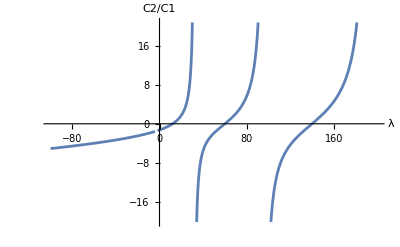

```mathematica
Plot[subleading,{λ,-100,200},AxesLabel->{"λ","C2/C1"}]
```

```mathematica
FindRoot[subleading==0,{λ,10}]
```

{λ→12.}

```mathematica
FindRoot[subleading==0,{λ,50}]
```

{λ→60.}

```mathematica
FindRoot[subleading==0,{λ,150}]
```

{λ→140.}

### Odd modes

Odd modes ~1/v at v==0

```mathematica
solc2=Assuming[λ ∈ Reals ,Solve[SeriesCoefficient[sZϕWorm,{v,0,2}]==0,C[2]]//Flatten//Simplify]
```

{C[2]→-8 ⅈ √(4+λ) Abs[λ] C[1]}

```mathematica
Assuming[λ >0,sZϕWorm/.solc2/.C[1]-> AA//FullSimplify]
```

(4 AA)/v+2 AA (-2+λ) v+O[v]^3

```mathematica
Assuming[λ <0,sZϕWorm/.solc2/.C[1]-> AA//FullSimplify]
```

(2 AA √(2+λ-√λ √(4+λ)) √(2+λ+√λ √(4+λ)))/v+(4 AA (-2+λ) v)/(√(2+λ-√λ √(4+λ)) √(2+λ+√λ √(4+λ)))+O[v]^3

Expansion about the (negative) boundary of the wormhole:

```mathematica
solzη[-1]
```

0

```mathematica
sZϕBoun=Series[solzη[v]/.solc2/.C[1]->AA,{v,-1,2}];
```

```mathematica
C1=SeriesCoefficient[sZϕBoun,1];
C2=SeriesCoefficient[sZϕBoun,2];
```

```mathematica
subleading=Assuming[λ  ∈ Reals,C2/C1-ratm1//Simplify//TrigToExp//Factor//FullSimplify]
```

(λ Tan[(4 π+π λ-(2 √2 (4+λ-√λ √(4+λ)) ArcTan[(√2)/(√(2+λ-√λ √(4+λ)))])/(√(2+λ-√λ √(4+λ)))-(2 √2 (4+λ+√λ √(4+λ)) ArcTan[(√2)/(√(2+λ+√λ √(4+λ)))])/(√(2+λ+√λ √(4+λ))))/(4 √(4+λ))])/(2 √(4+λ))

Asking the ratio C2/C1=1/2 corresponds to a vanishing subleading fall-off. Since we are working in the alternative quantization, this amounts to zero dual source.

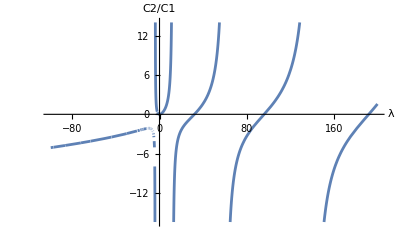

```mathematica
Plot[subleading,{λ,-100,200},AxesLabel->{"λ","C2/C1"}]
```

```mathematica
FindRoot[subleading==0,{λ,1/10},WorkingPrecision->40]
```

{λ→5.322413974741832029717788112542616498791×10^-21}

```mathematica
FindRoot[subleading==0,{λ,30}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{λ→32.}

```mathematica
FindRoot[subleading==0,{λ,90}]
```

{λ→96.}

```mathematica
FindRoot[subleading==0,{λ,190}]
```

{λ→192.}

d+1=5 Wormholes 𝒩==1^* SYM GPPZ, two scalars (Example 5)

Methodology:
This example involves two scalar fields and the coupled ODEs governing their fluctuations.

We first compactify the radial domain introducing a coordinate υ ∈ [-1,1]. The resulting ODE system has a singular point at υ = 0, which requires us to split the problem into two subdomains, υ ∈ [-1,0] and υ ∈ [0,1]. Since the two subproblems are identical, we restrict our analysis to the negative-υ domain. The solution in the positive-υ domain is determined by parity.

We then analyze the asymptotic behavior of the solutions at the two endpoints, υ = -1 and υ =0. This allows us to explicitly factor out the corresponding asymptotic behavior at each endpoint. We subsequently introduce a new radial coordinate s ∈ [-1,1]. 

We solve the coupled system numerically. Specifically, we match two numerical solutions propagated, respectively, from the two endpoints of the radial domain. We obtain the spectrum requiring the determinant of the matching matrix, constructed from the numerical solutions and their derivatives, to vanish at a specified point in the interior of the integration domain. This determinant constitutes a generalization of the Wronskian to the coupled system.

Notation:
- For ease of notation, the fields η^1 and η^2 in the paper are here denoted with χ and α, respectively.

## Background

Superpotential:

```mathematica
W[χ_,α_]=3/L (Cos[χ/(√3)]+Cos[α]);
```

Potential from superpotential:

```mathematica
d=4;
V[χ_,α_]=-1/2(D[ W[χ,α],χ]^2+D[ W[χ,α],α]^2)-d/(4(d-1))W[χ,α]^2//FullSimplify
```

-(3 (8-Cos[2 α]+8 Cos[α] Cos[χ/(√3)]+Cos[(2 χ)/(√3)]))/(4 L^2)

Background profile of the scalar ghosts:

```mathematica
χ0[r_]=2 √3 ArcTan[ⅇ^((r-r1)/L)];
α0[r_]=2ArcTan[ⅇ^(3(r-r2)/L)];
```

For convenience, we define the warp factor as a(r)≡e^(2A(r)), with

```mathematica
a[r_]=2^(4/3) Cosh[(r-r1)/L] Cosh[3 (r-r2)/L]^(1/3);
```

## Z_χ and Z_α fluctuation equations

We have already set the scalar, gauge-invariant combination of the metric to zero, H_S=0. We define the dimensionless eigenvalue λ≡L √(ω^2-k^2).

```mathematica
eqZχ=Collect[(2 a'[r] Zχ'[r])/a[r]+Zχ''[r]+Zα[r] (-1/(9 a'[r]^2)(2 χ0'[r] (α0'[r] (6 a'[r]^2+a[r]^2 (α0'[r]^2+χ0'[r]^2))+3 a[r] a'[r] Derivative[0,1][V][χ0[r],α0[r]])+6 a[r] a'[r] α0'[r] Derivative[1,0][V][χ0[r],α0[r]])+Derivative[1,1][V][χ0[r],α0[r]])+Zχ[r] ((-k^2+w^2)/a[r]-4/3 χ0'[r]^2-(2 a[r]^2 χ0'[r]^2 (α0'[r]^2+χ0'[r]^2))/(9 a'[r]^2)-(4 a[r] χ0'[r] Derivative[1,0][V][χ0[r],α0[r]])/(3 a'[r])+Derivative[2,0][V][χ0[r],α0[r]])/.{r1->0,r2->0}/.w->(√(λ+L^2 k^2))/L//TrigToExp//Simplify,{Zχ''[r],Zχ'[r],Zχ[r],Zα[r],λ},Simplify];
```

```mathematica
eqZα=Collect[(2 a'[r] Zα'[r])/a[r]+Zα''[r]+Zα[r] ((-k^2+w^2)/a[r]-4/3 α0'[r]^2-(2 a[r]^2 α0'[r]^2 (α0'[r]^2+χ0'[r]^2))/(9 a'[r]^2)-(4 a[r] α0'[r] Derivative[0,1][V][χ0[r],α0[r]])/(3 a'[r])+Derivative[0,2][V][χ0[r],α0[r]])+Zχ[r] (-1/(9 a'[r]^2)(2 χ0'[r] (α0'[r] (6 a'[r]^2+a[r]^2 (α0'[r]^2+χ0'[r]^2))+3 a[r] a'[r] Derivative[0,1][V][χ0[r],α0[r]])+6 a[r] a'[r] α0'[r] Derivative[1,0][V][χ0[r],α0[r]])+Derivative[1,1][V][χ0[r],α0[r]])/.{r1->0,r2->0}/.w->(√(λ+L^2 k^2))/L//TrigToExp//Simplify,{Zα''[r],Zα'[r],Zα[r],Zχ[r],λ},Simplify];
```

Change of radial coordinate (compactification):

```mathematica
rv[v_]=L/2 Log[(1+v)/(1-v)]; (* old coordinate as a function of the new coordinate *)
vr[rr_]=Solve[ⅇ^(2 rr/L)==(1+v)/(1-v),v][[1,1,2]]; (* new coordinate as a function of the old coordinate *)
Zχ[r_]=zχ[vr[r]];
Zα[r_]=zα[vr[r]];

eqzχ=Assuming[-1<v<1,Collect[Simplify[L^2/((1-v^2)^2)eqZχ/.r->rv[v]],{zχ''[v],zχ'[v],zχ[v],zα[v],λ},FullSimplify]]
eqzα=Assuming[-1<v<1,Collect[Simplify[L^2/((1-v^2)^2)eqZα/.r->rv[v]],{zα''[v],zα'[v],zα[v],zχ[v],λ},FullSimplify]]
```

(√3 (-1-5 v^2-11 v^4+v^6) zα[v])/(2 (1+3 v^2) (v+v^3)^2)+((-1+3 v^2+28 v^4+28 v^6+37 v^8+v^10)/(2 v^2 (1+3 v^2) (-1+v^4)^2)-λ/(2 (-1+v^2) (2+6 v^2)^(1/3))) zχ[v]+(2 v (3+v^2) zχ'[v])/(1+2 v^2-3 v^4)+zχ''[v]

((3 (-1-v^2+8 v^4+25 v^8+v^10))/(2 v^2 (1+3 v^2) (-1+v^4)^2)-λ/(2 (-1+v^2) (2+6 v^2)^(1/3))) zα[v]+(√3 (-1-5 v^2-11 v^4+v^6) zχ[v])/(2 (1+3 v^2) (v+v^3)^2)+(2 v (3+v^2) zα'[v])/(1+2 v^2-3 v^4)+zα''[v]

The equation is singular in v==0. The problem splits in two identical subproblems, negative v∈[-1,0] and positive v∈[0,1]. Let us consider the negative subproblem.

```mathematica
c1χ=Coefficient[eqzχ,zχ'[v]];
c0χ=Coefficient[eqzχ,zχ[v]];
d1χ=Coefficient[eqzχ,zα'[v]];
d0χ=Coefficient[eqzχ,zα[v]];

c1α=Coefficient[eqzα,zα'[v]];
c0α=Coefficient[eqzα,zα[v]];
d1α=Coefficient[eqzα,zχ'[v]];
d0α=Coefficient[eqzα,zχ[v]];
```

Asymptotic study about v==-1:

```mathematica
c1χvm1=Series[c1χ,{v,-1,-1}]
c0χvm1=Series[c0χ,{v,-1,-2}]
d1χvm1=Series[d1χ,{v,-1,-1}]
d0χvm1=Series[d0χ,{v,-1,-2}]
```

-1/(v+1)+O[v+1]^0

3/(4 (v+1)^2)+1/O[v+1]

0

O[v+1]^0

```mathematica
c1αvm1=Series[c1α,{v,-1,-1}]
c0αvm1=Series[c0α,{v,-1,-2}]
d1αvm1=Series[d1α,{v,-1,-1}]
d0αvm1=Series[d0α,{v,-1,-2}]
```

-1/(v+1)+O[v+1]^0

3/(4 (v+1)^2)+1/O[v+1]

0

O[v+1]^0

```mathematica
DSolve[{zχ''[v]+Normal[c1χvm1] zχ'[v]+Normal[c0χvm1] zχ[v]+Normal[d1χvm1] zα'[v]+Normal[d0χvm1] zα[v]==0,zα''[v]+Normal[c1αvm1] zα'[v]+Normal[c0αvm1] zα[v]+Normal[d1χvm1] zχ'[v]+Normal[d0χvm1] zχ[v]==0},{zχ[v],zα[v]},v]//Flatten
```

{zχ[v]→√(1+v) C[1]+(1+v)^(3/2) C[2],zα[v]→√(1+v) C[3]+(1+v)^(3/2) C[4]}

Asymptotic study about v==0:

```mathematica
c1χv0=Series[c1χ,{v,0,-1}]
c0χv0=Series[c0χ,{v,0,-2}]
d1χv0=Series[d1χ,{v,0,-1}]
d0χv0=Series[d0χ,{v,0,-2}]
```

O[v]^1

-1/(2 v^2)+1/O[v]

0

-(√3)/(2 v^2)+1/O[v]

```mathematica
c1αv0=Series[c1α,{v,0,-1}]
c0αv0=Series[c0α,{v,0,-2}]
d1αv0=Series[d1α,{v,0,-1}]
d0αv0=Series[d0α,{v,0,-2}]
```

O[v]^1

-3/(2 v^2)+1/O[v]

0

-(√3)/(2 v^2)+1/O[v]

```mathematica
DSolve[{zχ''[v]+Normal[c1χv0] zχ'[v]+Normal[c0χv0] zχ[v]+Normal[d1χv0] zα'[v]+Normal[d0χv0] zα[v]==0,zα''[v]+Normal[c1αv0] zα'[v]+Normal[c0αv0] zα[v]+Normal[d1χv0] zχ'[v]+Normal[d0χv0] zχ[v]==0},{zχ[v],zα[v]},v]//Flatten
```

{zα[v]→-C[1]/(6 v)+C[2]+v C[3]+v^2 C[4],zχ[v]→-C[1]/(6 √3 v)-√3 C[2]-√3 v C[3]+(v^2 C[4])/(√3)}

We factor out explicitly the subleading behaviours at both asymptotic regions:

```mathematica
eqzχe=eqzχ/.{zχ->zχe,zα->zαe};
eqzαe=eqzα/.{zχ->zχe,zα->zαe};
eqzχo=eqzχ/.{zχ->zχo,zα->zαo};
eqzαo=eqzα/.{zχ->zχo,zα->zαo};
```

```mathematica
zχe[v_]=(1-v^2)^(3/2)ψχve[v];
zαe[v_]=(1-v^2)^(3/2)ψαve[v];
zχo[v_]=1/v(1-v^2)^(3/2)ψχvo[v];
zαo[v_]=1/v(1-v^2)^(3/2)ψαvo[v];
```

We change the radial coordinate so that the domain coincides with s∈[-1,1].

```mathematica
vs[s_]=-Sqrt[(1-s)/2];
ψχve[v_]=ψχe[1-2 v^2];
ψαve[v_]=ψαe[1-2 v^2];
ψχvo[v_]=ψχo[1-2 v^2];
ψαvo[v_]=ψαo[1-2 v^2];
```

```mathematica
eqψχe=Assuming[-1<s<1,Collect[(eqzχe/.v->vs[s])/Coefficient[eqzχe/.v->vs[s]//Simplify,ψχe''[s]],{ψχe''[s],ψχe'[s],ψχe[s],ψαe[s],λ},Simplify]];
eqψαe=Assuming[-1<s<1,Collect[(eqzαe/.v->vs[s])/Coefficient[eqzαe/.v->vs[s]//Simplify,ψαe''[s]],{ψαe''[s],ψαe'[s],ψαe[s],ψχe[s],λ},Simplify]];
```

```mathematica
eqψχo=Assuming[-1<s<1,Collect[(eqzχo/.v->vs[s])/Coefficient[eqzχo/.v->vs[s],ψχo''[s]],{ψχo''[s],ψχo'[s],ψχo[s],ψαo[s],λ},Simplify]];
eqψαo=Assuming[-1<s<1,Collect[(eqzαo/.v->vs[s])/Coefficient[eqzαo/.v->vs[s],ψαo''[s]],{ψαo''[s],ψαo'[s],ψαo[s],ψχo[s],λ},Simplify]];
```

## Numerics, even modes (shooting and Wronksian matching)

We study the leading behavior of the equations at s==±1 so to relate the values of the solutions and their derivatives; this is needed because the numerical solver we are setting up needs two initial conditions for each field.

```mathematica
sauxψχem=Series[eqψχe,{s,-1,-1}]
sauxψαem=Series[eqψαe,{s,-1,-1}]
```

(1/32 (-16+λ) ψχe[-1]+2 ψχe'[-1])/(s+1)+O[s+1]^0

(1/32 (-24+λ) ψαe[-1]+2 ψαe'[-1])/(s+1)+O[s+1]^0

```mathematica
coefexpm={ψχe'[-1]/ψχe[-1],ψαe'[-1]/ψαe[-1]}/.Solve[{Normal[sauxψχem]==0,Normal[sauxψαem]==0}]/.{ψχe[-1]->ψχ0sm1, ψαe[-1]->ψα0sm1}//Simplify//Flatten
```

{1/4-λ/64,3/8-λ/64}

```mathematica
icχsm1[ψχ0sm1_,λ_,s_]=ψχ0sm1+coefexpm[[1]]ψχ0sm1 (s+1)
icαsm1[ψα0sm1_,λ_,s_]=ψα0sm1+coefexpm[[2]] ψα0sm1(s+1)
```

ψχ0sm1+(1+s) (1/4-λ/64) ψχ0sm1

ψα0sm1+(1+s) (3/8-λ/64) ψα0sm1

```mathematica
sauxψχe0=Series[eqψχe,{s,1,-1}]
sauxψαe0=Series[eqψαe,{s,1,-1}]
```

(-1/8 √3 ψαe[1]-ψχe[1]/8)/(s-1)^2+(-2^(2/3) λ ψχe[1]-4 √3 ψαe'[1]+12 ψχe'[1])/(32 (s-1))+O[s-1]^0

(-(3 ψαe[1])/8-1/8 √3 ψχe[1])/(s-1)^2+(-2^(2/3) λ ψαe[1]+4 ψαe'[1]-4 √3 ψχe'[1])/(32 (s-1))+O[s-1]^0

```mathematica
coefexp1={ψαe[1],ψαe'[1]}/.Solve[{SeriesCoefficient[sauxψχe0,-2]==0,SeriesCoefficient[sauxψαe0,-2]==0,SeriesCoefficient[sauxψχe0,-1]==0,SeriesCoefficient[sauxψαe0,-1]==0},{ψαe[1],ψαe'[1]}]/.{ψχe[1]->ψχ0s1,ψχe'[1]->dψχ0s1}//FullSimplify//Flatten
```

{-ψχ0s1/(√3),(12 dψχ0s1-2^(2/3) λ ψχ0s1)/(4 √3)}

```mathematica
coefexp10=D[coefexp1,ψχ0s1]
coefexp11=D[coefexp1,dψχ0s1]
```

{-1/(√3),-λ/(2 2^(1/3) √3)}

{0,√3}

```mathematica
icχs1[ψχ0s1_,dψχ0s1_,λ_,s_]=ψχ0s1+dψχ0s1 (s-1)
icαs1[ψχ0s1_,dψχ0s1_,λ_,s_]=(coefexp10[[1]]ψχ0s1+coefexp11[[1]]dψχ0s1)+(coefexp10[[2]]ψχ0s1+coefexp11[[2]] dψχ0s1) (s+1)
```

dψχ0s1 (-1+s)+ψχ0s1

-ψχ0s1/(√3)+(1+s) (√3 dψχ0s1-(λ ψχ0s1)/(2 2^(1/3) √3))

```mathematica
Clear[Aχ0,Aχ1,Bχ0,Bχ1,Cα0,Cα1]
Aχ0=Coefficient[eqψχe,ψχe'[s]]/.λ->0//Expand//FullSimplify
Aχ1=Coefficient[Coefficient[eqψχe,ψχe'[s]],λ]//Expand//FullSimplify

Bχ0=Coefficient[eqψχe,ψχe[s]]/.λ->0//Expand//FullSimplify
Bχ1=Coefficient[Coefficient[eqψχe,ψχe[s]],λ]//FullSimplify

Cα0=Coefficient[eqψχe,ψαe[s]]/.λ->0//Expand//FullSimplify
Cα1=Coefficient[Coefficient[eqψχe,ψαe[s]],λ]//FullSimplify
```

1/(2 (-1+s))+2/(1+s)+2/(-5+3 s)

0

(329+s (-780+s (678+s (-236+25 s))))/(8 (1+s) (-5+3 s) (3-4 s+s^2)^2)

1/((5-3 s)^(1/3) (8-8 s^2))

(√3 (49+s (-61+s (19+s))))/(8 (-5+3 s) (3-4 s+s^2)^2)

0

```mathematica
Clear[Aα0,Aα1,Bα0,Bα1,Cχ0,Cχ1]
Aα0=Coefficient[eqψαe,ψαe'[s]]/.λ->0//Expand//FullSimplify
Aα1=Coefficient[Coefficient[eqψαe,ψαe'[s]],λ]//Expand//FullSimplify

Bα0=Coefficient[eqψαe,ψαe[s]]/.λ->0//Expand//FullSimplify
Bα1=Coefficient[Coefficient[eqψαe,ψαe[s]],λ]//FullSimplify

Cχ0=Coefficient[eqψαe,ψχe[s]]/.λ->0//Expand//FullSimplify
Cχ1=Coefficient[Coefficient[eqψαe,ψχe[s]],λ]//FullSimplify
```

1/(2 (-1+s))+2/(1+s)+2/(-5+3 s)

0

(3 (-37+s (57+s (-31+3 s))))/(8 (1+s) (3-4 s+s^2)^2)

1/((5-3 s)^(1/3) (8-8 s^2))

(√3 (49+s (-61+s (19+s))))/(8 (-5+3 s) (3-4 s+s^2)^2)

0

```mathematica
eps=10^-9;
```

```mathematica
solBound[λ_?NumericQ,ψχ0sm1_?NumericQ,ψα0sm1_?NumericQ,ϵ_]:=NDSolveValue[{ψχ''[s]+(Aχ0+Aχ1 λ) ψχ'[s]+(Bχ0+Bχ1 λ) ψχ[s]+(Cα0+Cα1 λ) ψα[s]==0,ψα''[s]+(Aα0+Aα1 λ) ψα'[s]+(Bα0+Bα1 λ) ψα[s]+(Cχ0+Cχ1 λ) ψχ[s]==0,ψχ[-1+ϵ]==icχsm1[ψχ0sm1,λ,-1+ϵ],ψχ'[-1+ϵ]==D[icχsm1[ψχ0sm1,λ,s],s],ψα[-1+ϵ]==icαsm1[ψα0sm1,λ,-1+ϵ],ψα'[-1+ϵ]==D[icαsm1[ψα0sm1,λ,s],s]},{ψχ,ψχ',ψα,ψα'},{s,-1+ϵ,1/10},WorkingPrecision->40,AccuracyGoal->10,PrecisionGoal->10]
```

```mathematica
solThroat[λ_?NumericQ,ψχ0s1_?NumericQ,dψχ0s1_?NumericQ,ϵ_]:=NDSolveValue[{ψχ''[s]+(Aχ0+Aχ1 λ) ψχ'[s]+(Bχ0+Bχ1 λ) ψχ[s]+(Cα0+Cα1 λ) ψα[s]==0,ψα''[s]+(Aα0+Aα1 λ) ψα'[s]+(Bα0+Bα1 λ) ψα[s]+(Cχ0+Cχ1 λ) ψχ[s]==0,ψχ[1-ϵ]==icχs1[ψχ0s1,dψχ0s1,λ,1-ϵ],ψχ'[1-ϵ]==D[icχs1[ψχ0s1,dψχ0s1,λ,s],s],ψα[1-ϵ]==icαs1[ψχ0s1,dψχ0s1,λ,ϵ-1],ψα'[1-ϵ]==D[icαs1[ψχ0s1,dψχ0s1,λ,s],s]},{ψχ,ψχ',ψα,ψα'},{s,-1/10,1-ϵ},WorkingPrecision->40,AccuracyGoal->10,PrecisionGoal->10]
```

```mathematica
Wronsk[λ_?NumericQ,ϵ_]:=Module[{solB1,solB2,solT1,solT2,MM},
solB1=solBound[λ,1,0,ϵ];
solB2=solBound[λ,0,1,ϵ];
solT1=solThroat[λ,1,0,ϵ];
solT2=solThroat[λ,0,1,ϵ];
MM={{solB1[[1]][0],solB2[[1]][0],solT1[[1]][0],solT2[[1]][0]},{solB1[[2]][0],solB2[[2]][0],solT1[[2]][0],solT2[[2]][0]},
{solB1[[3]][0],solB2[[3]][0],solT1[[3]][0],solT2[[3]][0]},
{solB1[[4]][0],solB2[[4]][0],solT1[[4]][0],solT2[[4]][0]}
};
Det[MM]
]
```

```mathematica
Off[NDSolveValue::precw]
valsW=Table[{x,Wronsk[x,eps]},{x,-15,70,1}];
```

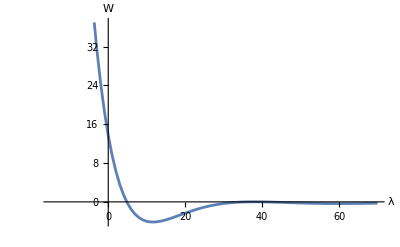

```mathematica
ListLinePlot[valsW,AxesLabel->{"λ","W"}]
```

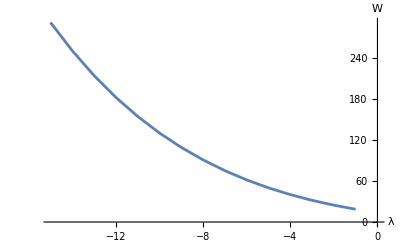
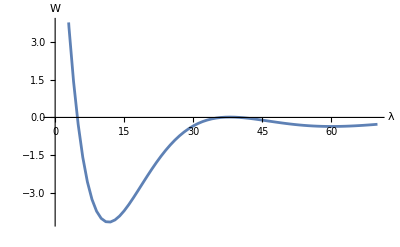

```mathematica
{ListLinePlot[valsW[[1;;15]],AxesLabel->{"λ","W"}],ListLinePlot[valsW[[15;;-1]],AxesLabel->{"λ","W"}]}
```

```mathematica
Chop[FindRoot[Wronsk[λ,eps]==0,{λ,5}]]
```

{λ→4.8205}

```mathematica
Chop[FindRoot[Wronsk[λ,eps]==0,{λ,35}]]
```

{λ→36.0513}

```mathematica
Chop[FindRoot[Wronsk[λ,eps]==0,{λ,90}]]
```

{λ→95.0173}

## Numerics, odd modes (shooting and Wronksian matching)

We study the leading behavior of the equations at s==±1 so to relate the values of the solutions and their derivatives; this is needed because the numerical solver we are setting up needs two initial conditions for each field.

```mathematica
sauxψχom=Series[eqψχo,{s,-1,-1}]
sauxψαom=Series[eqψαo,{s,-1,-1}]
```

(1/32 λ ψχo[-1]+2 ψχo'[-1])/(s+1)+O[s+1]^0

(1/32 (-8+λ) ψαo[-1]+2 ψαo'[-1])/(s+1)+O[s+1]^0

```mathematica
coefexpm={ψχo'[-1]/ψχo[-1],ψαo'[-1]/ψαo[-1]}/.Solve[{Normal[sauxψχom]==0,Normal[sauxψαom]==0},{ψχo'[-1],ψαo'[-1]}]/.{ψχo[-1]->ψχ0sm1, ψαo[-1]->ψα0sm1}//Simplify//Flatten
```

{-λ/64,(8-λ)/64}

```mathematica
icχsm1[ψχ0sm1_,λ_,s_]=ψχ0sm1+coefexpm[[1]]ψχ0sm1 (s+1)
icαsm1[ψα0sm1_,λ_,s_]=ψα0sm1+coefexpm[[2]] ψα0sm1(s+1)
```

ψχ0sm1-1/64 (1+s) λ ψχ0sm1

ψα0sm1+1/64 (1+s) (8-λ) ψα0sm1

```mathematica
sauxψχo0=Series[eqψχo,{s,1,-1}]
sauxψαo0=Series[eqψαo,{s,1,-1}]
```

(-1/8 √3 ψαo[1]+(3 ψχo[1])/8)/(s-1)^2+(-2^(2/3) λ ψχo[1]-4 √3 ψαo'[1]-4 ψχo'[1])/(32 (s-1))+O[s-1]^0

(ψαo[1]-√3 ψχo[1])/(8 (s-1)^2)+(-2^(2/3) λ ψαo[1]-12 ψαo'[1]-4 √3 ψχo'[1])/(32 (s-1))+O[s-1]^0

```mathematica
coefexp1={ψαo[1],ψαo'[1]}/.Solve[{SeriesCoefficient[sauxψχo0,-2]==0,SeriesCoefficient[sauxψαo0,-2]==0,SeriesCoefficient[sauxψχo0,-1]==0,SeriesCoefficient[sauxψαo0,-1]==0},{ψαo[1],ψαo'[1]}]/.{ψχo[1]->ψχ0s1,ψχo'[1]->dψχ0s1}//FullSimplify//Flatten
```

{√3 ψχ0s1,-(4 dψχ0s1+2^(2/3) λ ψχ0s1)/(4 √3)}

```mathematica
coefexp10=D[coefexp1,ψχ0s1]
coefexp11=D[coefexp1,dψχ0s1]
```

{√3,-λ/(2 2^(1/3) √3)}

{0,-1/(√3)}

```mathematica
icχs1[ψχ0s1_,dψχ0s1_,λ_,s_]=ψχ0s1+dψχ0s1 (s-1)
icαs1[ψχ0s1_,dψχ0s1_,λ_,s_]=(coefexp10[[1]]ψχ0s1+coefexp11[[1]]dψχ0s1)+(coefexp10[[2]]ψχ0s1+coefexp11[[2]] dψχ0s1) (s+1)
```

dψχ0s1 (-1+s)+ψχ0s1

√3 ψχ0s1+(1+s) (-dψχ0s1/(√3)-(λ ψχ0s1)/(2 2^(1/3) √3))

```mathematica
Clear[Aχ0,Aχ1,Bχ0,Bχ1,Cα0,Cα1]
Aχ0=Coefficient[eqψχo,ψχo'[s]]/.λ->0//Expand//FullSimplify
Aχ1=Coefficient[Coefficient[eqψχo,ψχo'[s]],λ]//Expand//FullSimplify

Bχ0=Coefficient[eqψχo,ψχo[s]]/.λ->0//Expand//FullSimplify
Bχ1=Coefficient[Coefficient[eqψχo,ψχo[s]],λ]//FullSimplify

Cα0=Coefficient[eqψχo,ψαo[s]]/.λ->0//Expand//FullSimplify
Cα1=Coefficient[Coefficient[eqψχo,ψαo[s]],λ]//FullSimplify
```

1/(2-2 s)+2/(1+s)+2/(-5+3 s)

0

(-139+5 s (35+(-13+s) s))/(8 (-5+3 s) (3-4 s+s^2)^2)

1/((5-3 s)^(1/3) (8-8 s^2))

(√3 (49+s (-61+s (19+s))))/(8 (-5+3 s) (3-4 s+s^2)^2)

0

```mathematica
Clear[Aα0,Aα1,Bα0,Bα1,Cχ0,Cχ1]
Aα0=Coefficient[eqψαo,ψαo'[s]]/.λ->0//Expand//FullSimplify
Aα1=Coefficient[Coefficient[eqψαo,ψαo'[s]],λ]//Expand//FullSimplify

Bα0=Coefficient[eqψαo,ψαo[s]]/.λ->0//Expand//FullSimplify
Bα1=Coefficient[Coefficient[eqψαo,ψαo[s]],λ]//FullSimplify

Cχ0=Coefficient[eqψαo,ψχo[s]]/.λ->0//Expand//FullSimplify
Cχ1=Coefficient[Coefficient[eqψαo,ψχo[s]],λ]//FullSimplify
```

1/(2-2 s)+2/(1+s)+2/(-5+3 s)

0

(87+s (-372+s (410+s (-148+7 s))))/(8 (-3+s)^2 (-1+s)^2 (1+s) (-5+3 s))

1/((5-3 s)^(1/3) (8-8 s^2))

(√3 (49+s (-61+s (19+s))))/(8 (-5+3 s) (3-4 s+s^2)^2)

0

```mathematica
eps=10^-9;
```

```mathematica
solBound[λ_?NumericQ,ψχ0sm1_?NumericQ,ψα0sm1_?NumericQ,ϵ_]:=NDSolveValue[{ψχ''[s]+(Aχ0+Aχ1 λ) ψχ'[s]+(Bχ0+Bχ1 λ) ψχ[s]+(Cα0+Cα1 λ) ψα[s]==0,ψα''[s]+(Aα0+Aα1 λ) ψα'[s]+(Bα0+Bα1 λ) ψα[s]+(Cχ0+Cχ1 λ) ψχ[s]==0,ψχ[-1+ϵ]==icχsm1[ψχ0sm1,λ,-1+ϵ],ψχ'[-1+ϵ]==D[icχsm1[ψχ0sm1,λ,s],s],ψα[-1+ϵ]==icαsm1[ψα0sm1,λ,-1+ϵ],ψα'[-1+ϵ]==D[icαsm1[ψα0sm1,λ,s],s]},{ψχ,ψχ',ψα,ψα'},{s,-1+ϵ,1/10},WorkingPrecision->40,AccuracyGoal->10,PrecisionGoal->10]
```

```mathematica
solThroat[λ_?NumericQ,ψχ0s1_?NumericQ,dψχ0s1_?NumericQ,ϵ_]:=NDSolveValue[{ψχ''[s]+(Aχ0+Aχ1 λ) ψχ'[s]+(Bχ0+Bχ1 λ) ψχ[s]+(Cα0+Cα1 λ) ψα[s]==0,ψα''[s]+(Aα0+Aα1 λ) ψα'[s]+(Bα0+Bα1 λ) ψα[s]+(Cχ0+Cχ1 λ) ψχ[s]==0,ψχ[1-ϵ]==icχs1[ψχ0s1,dψχ0s1,λ,1-ϵ],ψχ'[1-ϵ]==D[icχs1[ψχ0s1,dψχ0s1,λ,s],s],ψα[1-ϵ]==icαs1[ψχ0s1,dψχ0s1,λ,ϵ-1],ψα'[1-ϵ]==D[icαs1[ψχ0s1,dψχ0s1,λ,s],s]},{ψχ,ψχ',ψα,ψα'},{s,-1/10,1-ϵ},WorkingPrecision->40,AccuracyGoal->10,PrecisionGoal->10]
```

```mathematica
Wronsk[λ_?NumericQ,ϵ_]:=Module[{solB1,solB2,solT1,solT2,MM},
solB1=solBound[λ,1,0,ϵ];
solB2=solBound[λ,0,1,ϵ];
solT1=solThroat[λ,1,0,ϵ];
solT2=solThroat[λ,0,1,ϵ];
MM={{solB1[[1]][0],solB2[[1]][0],solT1[[1]][0],solT2[[1]][0]},{solB1[[2]][0],solB2[[2]][0],solT1[[2]][0],solT2[[2]][0]},
{solB1[[3]][0],solB2[[3]][0],solT1[[3]][0],solT2[[3]][0]},
{solB1[[4]][0],solB2[[4]][0],solT1[[4]][0],solT2[[4]][0]}
};
Det[MM]
]
```

```mathematica
Off[NDSolveValue::precw]
valsW=Table[{x,Wronsk[x,eps]},{x,-15,70,1}];
```

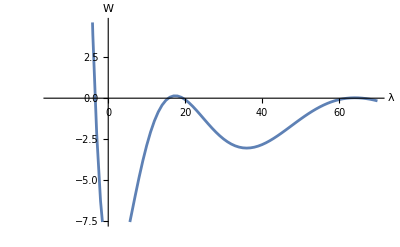

```mathematica
ListLinePlot[valsW,AxesLabel->{"λ","W"}]
```

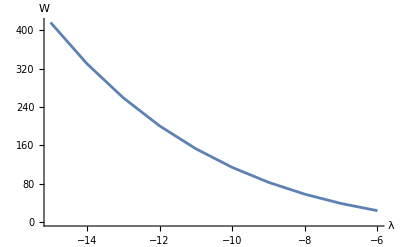
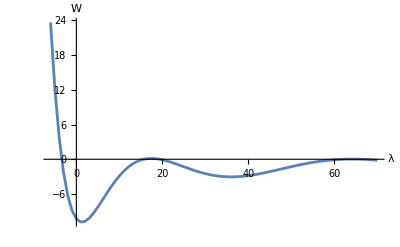

```mathematica
{ListLinePlot[valsW[[1;;10]],AxesLabel->{"λ","W"}],ListLinePlot[valsW[[10;;-1]],AxesLabel->{"λ","W"},PlotRange->All]}
```

```mathematica
Chop[FindRoot[Wronsk[λ,eps]==0,{λ,-3}]]
```

{λ→-3.40219}

```mathematica
Chop[FindRoot[Wronsk[λ,eps]==0,{λ,15}]]
```

{λ→15.6196}

```mathematica
Chop[FindRoot[Wronsk[λ,eps]==0,{λ,65}]]
```

{λ→66.1654}